```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]];
Clear[Header,FileData12,len,f];f=Import["entangled_tests2.csv"];
FileData12=Take[f,{2,3101}];Header=Take[f,1];Clear[f]; f=Import["entangled_tests.csv"];FileData13=Take[f,{2,3101}];Clear[f];Header
```

{{N,H1,H0,T1,T2,T3,T4 (max run),T5,T6(0),T8,K[+],K[-],Kdiff,PValue,Evalue,Keys,LCC Volts,Error}}

```mathematica
len12 = Length[FileData12];len13 = Length[FileData13];{len12,len13}
```

{3100,3100}

```mathematica
{55000,50000}
```

{55000,50000}

```mathematica
Err1=Select[FileData12,#[[18]]≠0 &]; Pe12=N[Length[Err1]/(len12*20000)];Join[Header, Err1] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | LCC Volts | Error
2330 | 0.999106 | 1.0517 | 10352 | 40.9088 | 161 | 14 | 2498 | 0.0176 | 2.72539 | 6.32456 | 1.73925 | 4.5853 | 0.76867 | 33.184 | 12 | 2.266 | 21)

```mathematica
Err2=Select[FileData13,#[[18]]≠0 &]; Pe13=N[Length[Err2]/(len13*20000)];Join[Header, Err2] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | LCC Volts | Error)

```mathematica
{Pe12,Pe13}
```

{1.6129×10^-8,0.}

```mathematica
{{Min[FileData12[[All,10]]],Max[FileData12[[All,10]]]},{Min[FileData13[[All,10]]],Max[FileData13[[All,10]]]}}//MatrixForm
```

(2.63921 | 2.78058
2.71418 | 2.82344)

```mathematica
{{Min[FileData12[[All,5]]],Max[FileData12[[All,5]]]},{Min[FileData13[[All,5]]],Max[FileData13[[All,5]]]}}//MatrixForm
```

(2.8544 | 53.5488
2.9568 | 43.3536)

```mathematica
{{Min[FileData12[[All,2]]],Min[FileData12[[All,3]]]},{Min[FileData13[[All,2]]],Min[FileData13[[All,3]]]}} // MatrixForm
```

(0.999106 | 0.9771
0.999311 | 0.956096)

```mathematica
{{Min[FileData12[[All,14]]],Max[FileData12[[All,14]]]},{Min[FileData13[[All,14]]],Max[FileData13[[All,14]]]}} // MatrixForm
```

(0.30412 | 1.
0.60679 | 1.)

```mathematica
Ent12=Select[FileData12,#[[2]]<0.99913 &];Ent13=Select[FileData13,#[[2]]<0.99913 &];{Length[Ent12],Length[Ent13]}
```

{1,0}

```mathematica
PVal12=Select[FileData12,#[[14]]<0.8&];PVal13=Select[FileData13,#[[14]]<0.8&];{Length[PVal12],Length[PVal13]}
```

{46,31}

```mathematica
K012=Select[FileData12,#[[13]]==0 &];K013=Select[FileData13,#[[13]]==0 &];{Length[K012],Length[K013]}
```

{123,141}

```mathematica
{Min[FileData12[[All,14]]],Max[FileData13[[All,14]]]}
```

{0.30412,1.}

```mathematica
P1=Select[FileData12,#[[14]]==1&];Length[P1]
```

33

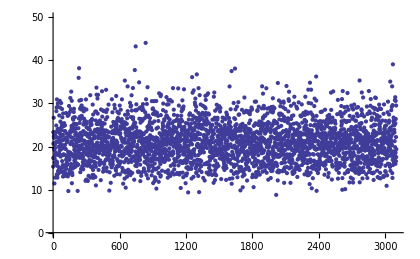
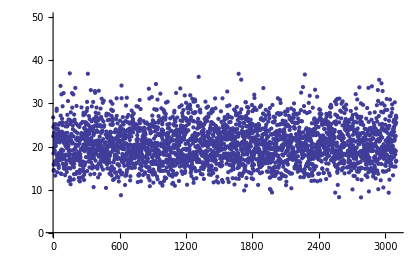
Chi Square Test (EValue) ENT | Chi Square Test (EValue) AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (EValue) ENT","Chi Square Test (EValue) AMP"},{ListPlot[FileData12[[All,15]],PlotRange->{0,50}, ImageSize->{420,300}],ListPlot[FileData13[[All,15]],PlotRange->{0,50},ImageSize->{420,300}]}} ,Frame->All]
```

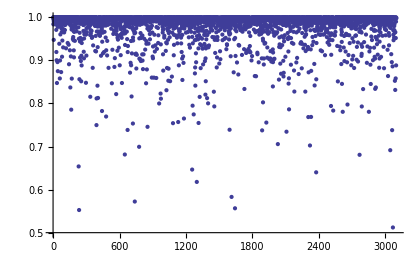
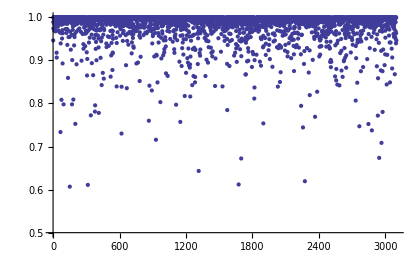
Chi Square Test (P-Value) QEKG I | Chi Square Test (P-Value) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (P-Value) QEKG I","Chi Square Test (P-Value) QEKG II"},{ListPlot[FileData12[[All,14]],PlotRange->{0.5,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,14]],PlotRange->{0.5,1},ImageSize->{420,300}]}} ,Frame->All]
```

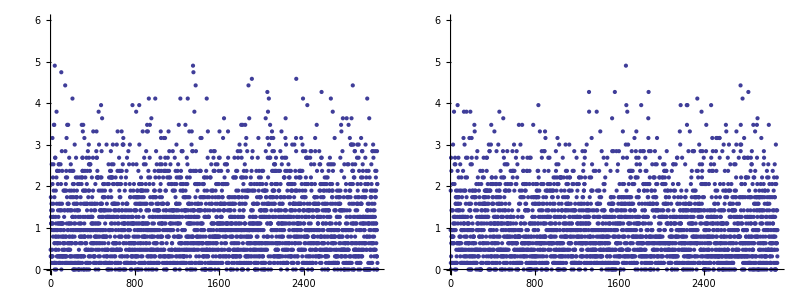

```mathematica
Grid[{{ListPlot[FileData12[[All,13]],PlotRange->{0,6}, ImageSize->{420,300}],ListPlot[FileData13[[All,13]],PlotRange->{0,6},ImageSize->{420,300}]}} ,Frame->All]
```

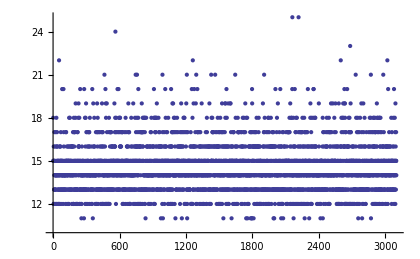
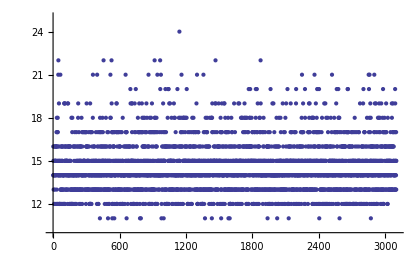
Max Run (Test 4) ENT | Max Run (Test 4) AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Max Run (Test 4) ENT","Max Run (Test 4) AMP"},{ListPlot[FileData12[[All,7]],PlotRange->{10,25}, ImageSize->{420,300}],ListPlot[FileData13[[All,7]],PlotRange->{10,25},ImageSize->{420,300}]}} ,Frame->All]
```

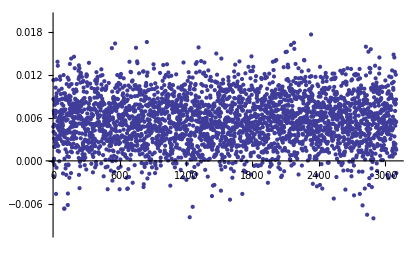
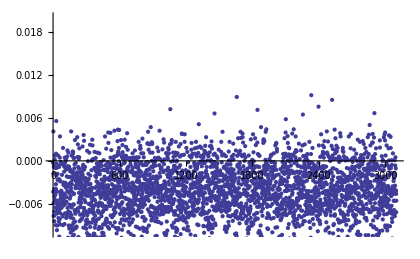
Test 6(0) ENT | Test 6(0) AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Test 6(0) ENT","Test 6(0) AMP"},{ListPlot[FileData12[[All,9]],PlotRange->{-0.01,0.02}, ImageSize->{420,300}],ListPlot[FileData13[[All,9]],PlotRange->{-0.01,0.02},ImageSize->{420,300}]}} ,Frame->All]
```

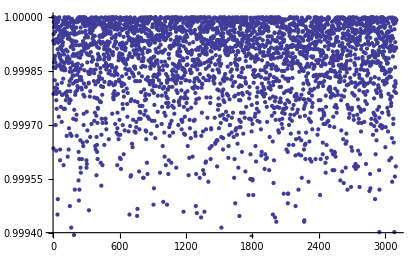
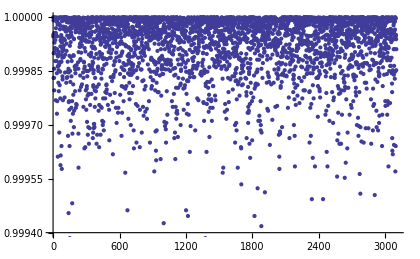
Entropy QEKG I | Entropy QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Entropy QEKG I","Entropy QEKG II"},{ListPlot[FileData12[[All,2]],PlotRange->{0.9994,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,2]],PlotRange->{0.9994,1},ImageSize->{420,300}]}} ,Frame->All]
```

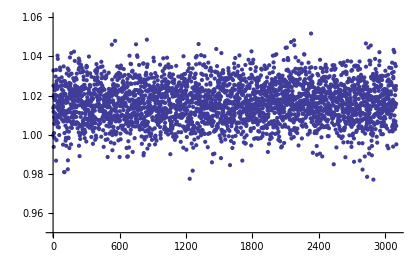
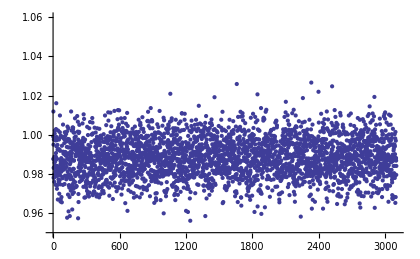
Entropy H0 ENT | Entropy H0 AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Entropy H0 ENT", "Entropy H0 AMP"},{ListPlot[FileData12[[All,3]],PlotRange->{0.95,1.06}, ImageSize->{420,300}],ListPlot[FileData13[[All,3]],PlotRange->{0.95,1.06},ImageSize->{420,300}]}} ,Frame->All]
```

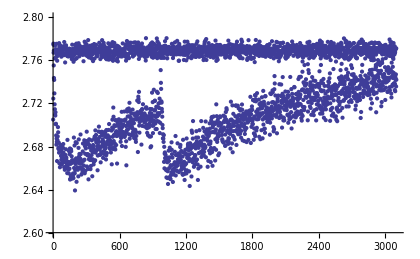
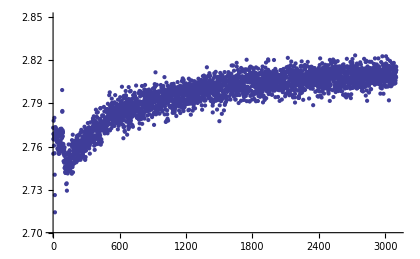
Test 8 ENT | Test 8 AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Test 8 ENT","Test 8 AMP"},{ListPlot[FileData12[[All,10]],PlotRange->{2.6,2.8}, ImageSize->{420,300}],ListPlot[FileData13[[All,10]],PlotRange->{2.7,2.85},ImageSize->{420,300}]}} ,Frame->All]
```

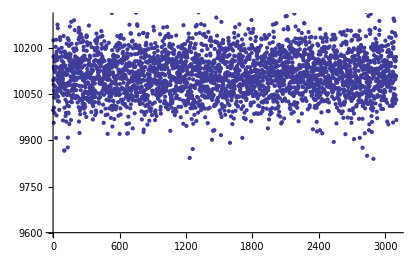
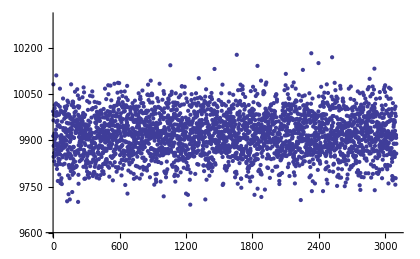
Monobit Test [FI140-1] (T1) QEKG I | Monobit Test [FI140-1] (T1) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Monobit Test [FI140-1] (T1) QEKG I", "Monobit Test [FI140-1] (T1) QEKG II"},{ListPlot[FileData12[[All,4]],PlotRange->{9600,10300}, ImageSize->{420,300}],ListPlot[FileData13[[All,4]],PlotRange->{9600,10300},ImageSize->{420,300}]}} ,Frame->All]
```

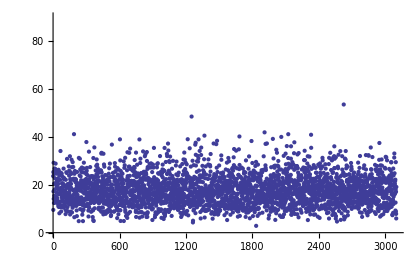
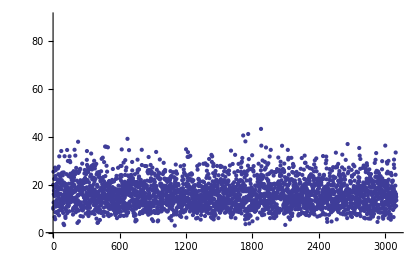
Block Test (T2) QEKG I | Block Test (T2) QEKG II
-Graphics- | -Graphics-

```mathematica
Grid[{{"Block Test (T2) QEKG I", "Block Test (T2) QEKG II"},{ListPlot[FileData12[[All,5]],PlotRange->{0,90}, ImageSize->{420,300}],ListPlot[FileData13[[All,5]],PlotRange->{0,90},ImageSize->{420,300}]}} ,Frame->All]
```

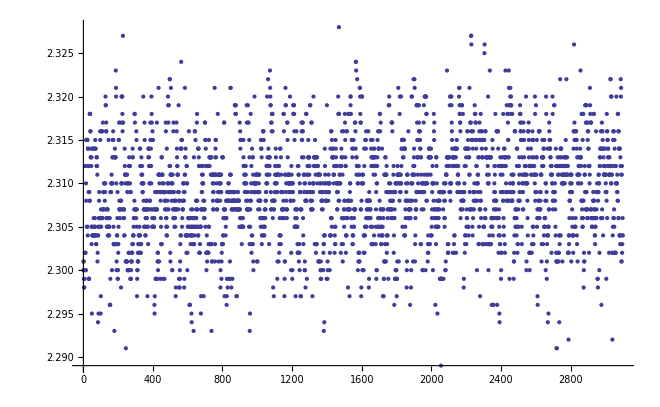

```mathematica
ListPlot[FileData13[[All,17]],PlotRange->{All}, ImageSize->{660,500}]
```